```mathematica
a1=12;
a2=12;
a3=8;
a4=8.5;
d3=8;
tpp=1.9; (*time range*)
tstep=0.001;  (*time step*)
tpath=2t+6;(*time dependent function*)
tdpath=1;(*time dependent function derivative*)
tddpath=0;
q1value=35;
q2value=55;
q3value=-40;
q4value=50;
q1=Table[(47+q1value)*tpath*π/180,{t,1,tpp,tstep}];
q2=Table[(191+q2value)*tpath*π/180,{t,1,tpp,tstep}];
q3=Table[(164+q3value)*tpath*π/180,{t,1,tpp,tstep}];
q4=Table[(180+q4value)*tpath*π/180,{t,1,tpp,tstep}];
q1d=Table[q1value*tdpath*π/180,{t,1,tpp,tstep}];
q2d=Table[q2value*tdpath*π/180,{t,1,tpp,tstep}];
q3d=Table[q3value*tdpath*π/180,{t,1,tpp,tstep}];
q4d=Table[q4value*tdpath*π/180,{t,1,tpp,tstep}];
q1dd=Table[q1value*tddpath*π/180,{t,1,tpp,tstep}];
q2dd=Table[q2value*tddpath*π/180,{t,1,tpp,tstep}];
q3dd=Table[q3value*tddpath*π/180,{t,1,tpp,tstep}];
q4dd=Table[q4value*tddpath*π/180,{t,1,tpp,tstep}];
m1=0.07;
m2=0.07;
m3=0.05;
m4=0.05;
T1=1/24 (m4 q4dd (-12 a2 a3+a4^2-6 a1 a2 Cos[q2-q3]-12 a2^2 Cos[q3]-6 a1 a2 Cos[q2+q3]+a4^2 Cos[2 (q3-q4)]-6 a2 a4 Cos[q4])-q3dd (-a3^2 m3+12 a2 a3 m4-a4^2 m4+24 a1 a3 m4 Cos[q2]+18 a1 a2 m4 Cos[q2-q3]+24 a1^2 m4 Cos[q3]+12 a2^2 m4 Cos[q3]+a3^2 m3 Cos[2 q3]+18 a1 a2 m4 Cos[q2+q3]+6 a1 a4 m4 Cos[q2-q4]-a4^2 m4 Cos[2 (q3-q4)]+6 a2 a4 m4 Cos[q4]+6 a1 a4 m4 Cos[q2+q4])-48 a1^2 m4 Cos[q2]^2 (q2d^2+q1d q3d Cos[q3]) Sin[q3]+q1dd (8 a1^2 m1+24 a1^2 m2+8 a2^2 m2+12 a1^2 m3+24 a2^2 m3+25 a3^2 m3+24 d3^2 m3+18 a1^2 m4+12 a2^2 m4+24 a3^2 m4+4 a4^2 m4+24 a1 a2 (m2+2 m3+m4) Cos[q2]+6 a1^2 (2 m3-m4) Cos[2 q2]+12 a1 a2 m4 Cos[q2-2 q3]+24 a1 a3 m3 Cos[q2-q3]+24 a1 a3 m4 Cos[q2-q3]+3 a1^2 m4 Cos[2 (q2-q3)]+48 a2 a3 m3 Cos[q3]+48 a2 a3 m4 Cos[q3]-a3^2 m3 Cos[2 q3]+6 a1^2 m4 Cos[2 q3]+12 a2^2 m4 Cos[2 q3]+24 a1 a3 m3 Cos[q2+q3]+24 a1 a3 m4 Cos[q2+q3]+3 a1^2 m4 Cos[2 (q2+q3)]+12 a1 a2 m4 Cos[q2+2 q3]+6 a1 a4 m4 Cos[q2-q3-q4]+12 a2 a4 m4 Cos[q3-q4]+a4^2 m4 Cos[2 (q3-q4)]+6 a1 a4 m4 Cos[q2+q3-q4]+24 a3 a4 m4 Cos[q4]+3 a4^2 m4 Cos[2 q4]+6 a1 a4 m4 Cos[q2-q3+q4]+12 a2 a4 m4 Cos[q3+q4]+6 a1 a4 m4 Cos[q2+q3+q4]+24 a1 d3 m3 Sin[q2-q3]-48 a2 d3 m3 Sin[q3]-24 a1 d3 m3 Sin[q2+q3])+q2dd (8 a2^2 m2+a3^2 m3+a4^2 m4+12 a1 a2 m2 Cos[q2]-12 a1 (a3 m3+a2 m4) Cos[q2-q3]-6 a1^2 m4 Cos[2 q2-q3]-a3^2 m3 Cos[2 q3]+12 a1 a3 m3 Cos[q2+q3]+12 a1 a2 m4 Cos[q2+q3]+6 a1^2 m4 Cos[2 q2+q3]+a4^2 m4 Cos[2 (q3-q4)]+12 a1 d3 m4 Sin[q2]-12 a1 d3 m3 Sin[q2-q3]-12 a1 d3 m3 Sin[q2+q3])-24 a1 Cos[q2] (-d3 m4 q2d^2+4 a1 m3 q1d q2d Sin[q2]+2 a3 m3 q2d^2 Sin[q3]+2 a2 m4 q2d^2 Sin[q3]+4 a3 m3 q1d q3d Sin[q3]+4 a3 m4 q1d q3d Sin[q3]-a2 m4 q3d q4d Sin[q3]+2 a4 m4 q1d q3d Cos[q4] Sin[q3]-a4 m4 q3d q4d Sin[q4]+2 Cos[q3] (d3 m3 q2d^2+2 d3 m3 q1d q3d+a1 m4 q2d q3d Sin[q2]+4 a2 m4 q1d q3d Sin[q3]+a4 m4 q1d q4d Sin[q4]))+4 (6 a1^2 m4 q1d q2d Sin[2 q2]-6 a1^2 m4 q1d q2d Cos[2 q3] Sin[2 q2]-9 a1 a2 m4 q3d^2 Sin[q2-q3]+3 a1 a2 m4 q2d q4d Sin[q2-q3]-24 a2 a3 m3 q1d q3d Sin[q3]-24 a2 a3 m4 q1d q3d Sin[q3]+12 a1^2 m4 q3d^2 Sin[q3]+6 a2^2 m4 q3d^2 Sin[q3]+6 a2^2 m4 q3d q4d Sin[q3]-12 a2 a4 m4 q1d q3d Cos[q4] Sin[q3]+12 a1^2 m4 q2d^2 Sin[q2]^2 Sin[q3]-6 a1 q2d Sin[q2] (2 a2 m2 q1d+4 a2 m3 q1d+a2 m4 q1d+a2 m2 q2d-2 a3 m4 q3d+a2 m4 q1d Cos[2 q3]-a4 m4 q3d Cos[q4]-4 d3 m3 q1d Sin[q3]-2 d3 m3 q3d Sin[q3])+a3^2 m3 q1d q3d Sin[2 q3]-12 a2^2 m4 q1d q3d Sin[2 q3]+a3^2 m3 q2d q3d Sin[2 q3]+a3^2 m3 q3d^2 Sin[2 q3]-3 a1^2 m4 q1d q3d Cos[2 q2] Sin[2 q3]+a4^2 m4 q1d q4d Cos[q4]^2 Sin[2 q3]-a4^2 m4 q1d q3d Cos[2 q4] Sin[2 q3]+9 a1 a2 m4 q3d^2 Sin[q2+q3]+3 a1 a2 m4 q2d q4d Sin[q2+q3]-a4^2 m4 q2d q3d Sin[2 (q3-q4)]-a4^2 m4 q3d^2 Sin[2 (q3-q4)]+a4^2 m4 q2d q4d Sin[2 (q3-q4)]+a4^2 m4 q4d^2 Sin[2 (q3-q4)]-12 a3 a4 m4 q1d q4d Sin[q4]+3 a2 a4 m4 q3d q4d Sin[q4]+3 a2 a4 m4 q4d^2 Sin[q4]-a4^2 m4 q1d q4d Cos[2 q3-q4] Sin[q4]-5 a4^2 m4 q1d q4d Cos[q4] Sin[q4]-2 a4^2 m4 q1d q3d Cos[q4] Sin[q3]^2 Sin[q4]-6 Cos[q3] (a1 q2d (4 a3 m3 q1d+4 a3 m4 q1d+2 a3 m3 q3d-a2 m4 q3d+2 a4 m4 q1d Cos[q4]) Sin[q2]+q1d (4 a2 d3 m3 q3d+a1^2 m4 q3d Sin[q3]+2 a2 a4 m4 q4d Sin[q4]))-m4 q1d Cos[q3]^2 (12 a1 a2 q2d Sin[q2]+a4^2 (-q3d+q4d) Sin[2 q4])));
T2=1/24 (2 a4^2 m4 q4dd Cos[q3-q4]^2+q1dd (8 a2^2 m2+a3^2 m3+a4^2 m4+12 a1 a2 m2 Cos[q2]-12 a1 (a3 m3+a2 m4) Cos[q2-q3]-6 a1^2 m4 Cos[2 q2-q3]-a3^2 m3 Cos[2 q3]+12 a1 a3 m3 Cos[q2+q3]+12 a1 a2 m4 Cos[q2+q3]+6 a1^2 m4 Cos[2 q2+q3]+a4^2 m4 Cos[2 (q3-q4)]+12 a1 d3 m4 Sin[q2]-12 a1 d3 m3 Sin[q2-q3]-12 a1 d3 m3 Sin[q2+q3])+q2dd (8 a2^2 m2+24 a1^2 m3+24 a2^2 m3+a3^2 m3+12 a1^2 m4+24 a2^2 m4+6 a3^2 m4+a4^2 m4+6 d3^2 m4+48 a1 a2 (m3+m4) Cos[q2]+12 a1^2 m4 Cos[2 q2]+12 a1 a3 m4 Cos[q2-q3]+24 a2 a3 m4 Cos[q3]-a3^2 m3 Cos[2 q3]+12 a1 a3 m4 Cos[q2+q3]+a4^2 m4 Cos[2 (q3-q4)]+12 a1 d3 m4 Sin[q2-q3]-24 a2 d3 m4 Sin[q3]-12 a1 d3 m4 Sin[q2+q3])+q3dd (12 a2^2 m3+a3^2 m3+a4^2 m4+12 a1 a2 m3 Cos[q2]-6 a1 a3 m4 Cos[q2-q3]-a3^2 m3 Cos[2 q3]+6 a1 a3 m4 Cos[q2+q3]+a4^2 m4 Cos[2 (q3-q4)]-6 a1 d3 m4 Sin[q2-q3]-6 a1 d3 m4 Sin[q2+q3])+4 (-3 a1 d3 m4 (2 q2d-q3d) q3d Cos[q2-q3]-6 a1 d3 m4 q2d q3d Cos[q2+q3]-3 a1 d3 m4 q3d^2 Cos[q2+q3]+6 a1 a2 m2 q1d^2 Sin[q2]+12 a1 a2 m3 q1d^2 Sin[q2]+6 a1 a2 m4 q1d^2 Sin[q2]-12 a1 a2 m3 q2d^2 Sin[q2]-12 a1 a2 m4 q2d^2 Sin[q2]-12 a1 a3 m4 q1d q3d Sin[q2]+6 a1 a2 m4 q3d^2 Sin[q2]+6 a1 a2 m4 q3d q4d Sin[q2]-6 a1^2 m4 q1d^2 Cos[q2] Sin[q2]+6 a1 a2 m4 q1d^2 Cos[q3]^2 Sin[q2]-6 a1 a4 m4 q1d q3d Cos[q4] Sin[q2]+6 a1 Cos[q3] (a3 m4 (2 q1d^2-q2d^2)+2 a3 m3 q1d (q1d-q3d)-5 a2 m4 q1d q3d+a4 m4 q1d^2 Cos[q4]) Sin[q2]+6 a1^2 m3 q1d^2 Sin[2 q2]-6 a1^2 m4 q2d^2 Sin[2 q2]+3 a1^2 m4 q1d^2 Cos[2 q3] Sin[2 q2]-6 m4 q3d Cos[q3] (2 a2 d3 q2d+a1^2 q1d Sin[2 q2])+6 a1 a3 m4 q2d q3d Sin[q2-q3]-3 a1 a3 m4 q3d^2 Sin[q2-q3]-3 a1 a2 m4 q1d q4d Sin[q2-q3]-12 a2 a3 m4 q2d q3d Sin[q3]-12 a1 d3 m3 q1d^2 Sin[q2] Sin[q3]+6 a1 d3 m4 q2d^2 Sin[q2] Sin[q3]+12 a1 d3 m3 q1d q3d Sin[q2] Sin[q3]-6 a1 a2 m4 q1d^2 Sin[q2] Sin[q3]^2+a3^2 m3 q1d q3d Sin[2 q3]+a3^2 m3 q2d q3d Sin[2 q3]+a3^2 m3 q3d^2 Sin[2 q3]-6 a1 a3 m4 q2d q3d Sin[q2+q3]-3 a1 a3 m4 q3d^2 Sin[q2+q3]-3 a1 a2 m4 q1d q4d Sin[q2+q3]-a4^2 m4 q1d q3d Sin[2 (q3-q4)]-a4^2 m4 q2d q3d Sin[2 (q3-q4)]-a4^2 m4 q3d^2 Sin[2 (q3-q4)]+a4^2 m4 q1d q4d Sin[2 (q3-q4)]+a4^2 m4 q2d q4d Sin[2 (q3-q4)]+a4^2 m4 q4d^2 Sin[2 (q3-q4)]));
T3=1/24 (m4 q4dd (6 a2^2+a4^2+12 a1 a2 Cos[q2]+a4^2 Cos[2 (q3-q4)])+q3dd (6 a2^2 m3+a3^2 m3+24 a1^2 m4+6 a2^2 m4+a4^2 m4+24 a1 a2 m4 Cos[q2]-a3^2 m3 Cos[2 q3]+a4^2 m4 Cos[2 (q3-q4)])-q1dd (-a3^2 m3+12 a2 a3 m4-a4^2 m4+24 a1 a3 m4 Cos[q2]+18 a1 a2 m4 Cos[q2-q3]+24 a1^2 m4 Cos[q3]+12 a2^2 m4 Cos[q3]+a3^2 m3 Cos[2 q3]+18 a1 a2 m4 Cos[q2+q3]+6 a1 a4 m4 Cos[q2-q4]-a4^2 m4 Cos[2 (q3-q4)]+6 a2 a4 m4 Cos[q4]+6 a1 a4 m4 Cos[q2+q4])+q2dd (12 a2^2 m3+a3^2 m3+a4^2 m4+12 a1 a2 m3 Cos[q2]-6 a1 a3 m4 Cos[q2-q3]-a3^2 m3 Cos[2 q3]+6 a1 a3 m4 Cos[q2+q3]+a4^2 m4 Cos[2 (q3-q4)]-6 a1 d3 m4 Sin[q2-q3]-6 a1 d3 m4 Sin[q2+q3])+2 (6 a1 a2 m4 q1d q4d Sin[q2-q3]+24 a2 a3 m3 q1d^2 Sin[q3]+24 a2 a3 m4 q1d^2 Sin[q3]+12 a2 a3 m4 q2d^2 Sin[q3]-12 a2^2 m4 q1d q4d Sin[q3]+24 a1 a3 m3 q1d^2 Cos[q2] Sin[q3]+24 a1 a3 m4 q1d^2 Cos[q2] Sin[q3]+12 a2 a4 m4 q1d^2 Cos[q4] Sin[q3]+12 a1 a4 m4 q1d^2 Cos[q2] Cos[q4] Sin[q3]-12 a1 q2d Sin[q2] (-2 a3 m4 q1d+a2 m3 q2d+2 a2 m4 q3d+a2 m4 q4d-a4 m4 q1d Cos[q4]+2 d3 m3 q1d Sin[q3])+2 Cos[q3] (12 a2 d3 m3 q1d^2+6 a2 d3 m4 q2d^2+6 a1 (2 a3 m3+5 a2 m4) q1d q2d Sin[q2]+6 a1^2 m4 q1d q2d Sin[2 q2]-a3^2 m3 q1d^2 Sin[q3]+3 a1^2 m4 q1d^2 Sin[q3]-a3^2 m3 q2d^2 Sin[q3]+12 a1 q1d^2 Cos[q2] (d3 m3+2 a2 m4 Sin[q3]))+12 a2^2 m4 q1d^2 Sin[2 q3]-2 a3^2 m3 q1d q2d Sin[2 q3]+a3^2 m3 q3d^2 Sin[2 q3]+6 a1^2 m4 q1d^2 Cos[q2]^2 Sin[2 q3]+3 a1^2 m4 q1d^2 Cos[2 q2] Sin[2 q3]+a4^2 m4 q1d^2 Cos[2 q4] Sin[2 q3]-6 a1 a2 m4 q1d q4d Sin[q2+q3]-6 a1 a4 m4 q1d q4d Sin[q2-q4]+2 a4^2 m4 q1d q2d Sin[2 (q3-q4)]+a4^2 m4 q2d^2 Sin[2 (q3-q4)]-a4^2 m4 q3d^2 Sin[2 (q3-q4)]+4 a4^2 m4 q1d q4d Sin[2 (q3-q4)]+4 a4^2 m4 q2d q4d Sin[2 (q3-q4)]+2 a4^2 m4 q3d q4d Sin[2 (q3-q4)]+3 a4^2 m4 q4d^2 Sin[2 (q3-q4)]+6 a2 a4 m4 q1d q4d Sin[q4]-2 a4^2 m4 q1d^2 Cos[q3]^2 Cos[q4] Sin[q4]+a4^2 m4 q1d^2 Sin[q3]^2 Sin[2 q4]+6 a1 a4 m4 q1d q4d Sin[q2+q4]));
T4=1/24 m4 (2 a4^2 q2dd Cos[q3-q4]^2+q4dd (6 a2^2+a4^2+a4^2 Cos[2 (q3-q4)])+q3dd (6 a2^2+a4^2+12 a1 a2 Cos[q2]+a4^2 Cos[2 (q3-q4)])+q1dd (-12 a2 a3+a4^2-6 a1 a2 Cos[q2-q3]-12 a2^2 Cos[q3]-6 a1 a2 Cos[q2+q3]+a4^2 Cos[2 (q3-q4)]-6 a2 a4 Cos[q4])+2 (q2d (3 a1 a2 q1d Sin[q2-q3]+3 a1 a2 q1d Sin[q2+q3]-a4^2 (q1d+q2d+3 q3d) Sin[2 (q3-q4)])-q3d (6 a1 a2 q2d Sin[q2]+a4 (a4 (2 q2d+3 q3d+q4d) Sin[2 (q3-q4)]+6 a1 q1d Cos[q2] Sin[q4]))+q4d (q2d (3 a1 a2 Sin[q2-q3]+3 a1 a2 Sin[q2+q3]+a4^2 Sin[2 (q3-q4)])+2 a4 q4d (a4 Sin[2 (q3-q4)]+3 a2 Sin[q4])+3 q3d (2 a2 (a2+a1 Cos[q2]) Sin[q3]+a4 (a2+2 a1 Cos[q2]) Sin[q4])-a4 q1d ((12 a3+a4 Cos[2 q3-q4]+5 a4 Cos[q4]) Sin[q4]-2 Cos[q3] (a4 Cos[q4]^2 Sin[q3]-6 (a2+a1 Cos[q2]) Sin[q4])+a4 Cos[q3]^2 Sin[2 q4]))+q1d (q2d (3 a1 a2 Sin[q2-q3]+3 a1 a2 Sin[q2+q3]-a4^2 Sin[2 (q3-q4)])+a4 q1d ((12 a3+a4 Cos[2 q3-q4]+5 a4 Cos[q4]) Sin[q4]-2 Cos[q3] (a4 Cos[q4]^2 Sin[q3]-6 (a2+a1 Cos[q2]) Sin[q4])+a4 Cos[q3]^2 Sin[2 q4])-q3d (3 a1 a2 Sin[q2-q3]-6 a2^2 Sin[q3]-3 a1 a2 Sin[q2+q3]-3 a1 a4 Sin[q2-q4]+2 a4^2 Sin[2 (q3-q4)]+3 a2 a4 Sin[q4]+3 a1 a4 Sin[q2+q4]))));
```

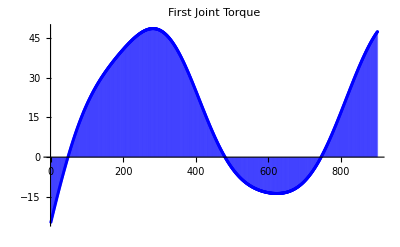

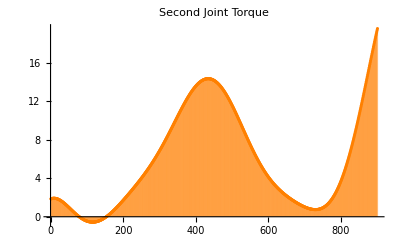

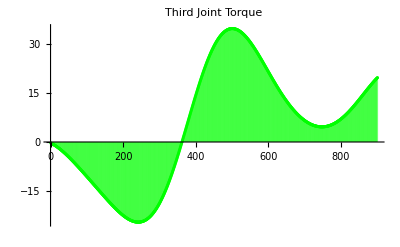

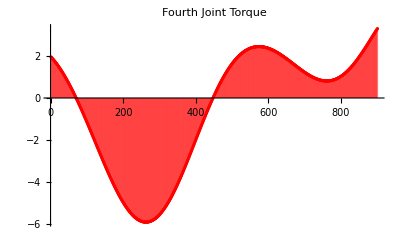

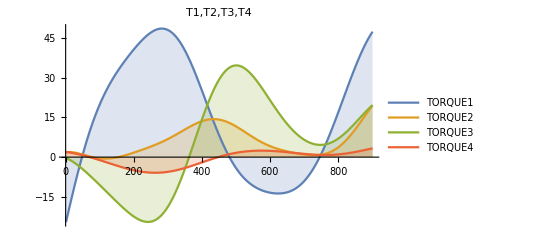

```mathematica
(*Plotting Torque 1*)
ListPlot[T1,PlotLabel->"First Joint Torque",Filling->Axis,PlotStyle->Directive[Blue]]
(*Plotting Torque 2*)
ListPlot[T2,PlotLabel->"Second Joint Torque",Filling->Axis,PlotStyle->Directive[Orange]]
(*Plotting Torque 3*)
ListPlot[T3,PlotLabel->"Third Joint Torque",Filling->Axis,PlotStyle->Directive[Green]]
(*Plotting Torque 4*)
ListPlot[T4,PlotLabel->"Fourth Joint Torque",Filling->Axis,PlotStyle->Directive[Red]]
(*Plotting Torque1,Torque2,Torque3,Torque4 *)
ListLinePlot[{T1,T2,T3,T4},Filling->Axis,PlotLegends->{"TORQUE1","TORQUE2","TORQUE3"
,"TORQUE4"},PlotLabel->"T1,T2,T3,T4"]

(*ListLinePlot[Labeled[T1,"T1"],Labeled[T2,"T2"],PlotLayout->"Row"]*)
```